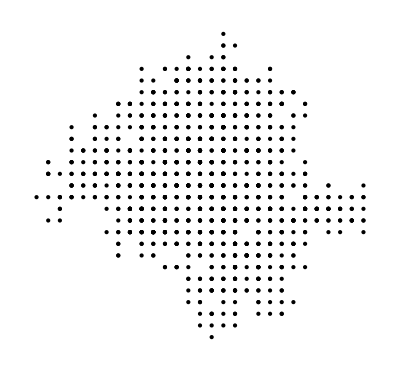

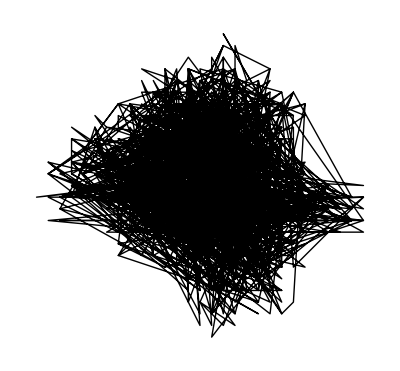

```mathematica
cluster={{0,0}};
next=Nearest[cluster->Automatic];
wander:=RandomChoice[{{0,1},{1,0},{0,-1},{-1,0}}];
ncluster=1200;
l=100;

Do[particle=RandomInteger[{-l,l},2];
While[Length[next[particle,{1,1}]]==0,particle=RandomInteger[{-l+1,l-1},2];];
step=wander;
While[Length[next[particle,{1,1}]]==0,particle+=step;
step=wander;
While[!inBounds[particle+step,l],step=wander;]];
AppendTo[cluster,particle];
next=Nearest[cluster->Automatic],{ncluster}];

Graphics[{Point[cluster]}]
Graphics[{Line[cluster]}]
Graphics[{Text[cluster]}]
```

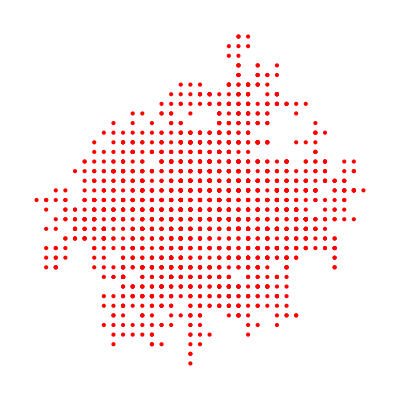

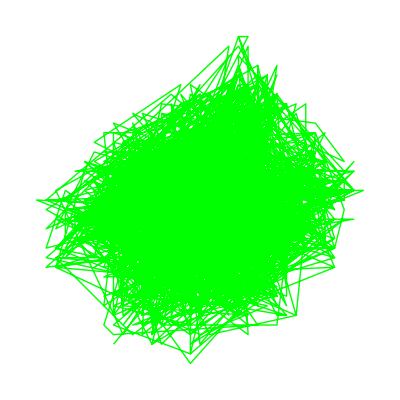

-Graphics-

```mathematica
cluster={{0,0}};
next=Nearest[cluster->Automatic];
wander:=RandomChoice[{{0,1},{1,0},{0,-1},{-1,0}}];
ncluster=2000;

Do[particle=RandomInteger[{-l,l},2];
While[Length[next[particle,{1,1}]]==0,particle=RandomInteger[{-l+1,l-1},2];];
step=wander;
While[Length[next[particle,{1,1}]]==0,particle+=step;
step=wander;
While[!inBounds[particle+step,l],step=wander;]];
AppendTo[cluster,particle];
next=Nearest[cluster->Automatic],{ncluster}];

p= cluster;

Graphics[{Red,Point[p]}]
Graphics[{Green, Line[p]}]
Graphics[{Text[p]}]
```